```mathematica
Needs["ErrorBarPlots`"]
LinReg[daten_]:=Module[{x,y,Δy,S,Δa0,Δb0,a0,b0,n,squadrat,ymitt,Rquadrat,Χquadrat},
n=Length[daten];
x=daten[[All,1]];
y=daten[[All,2]];
Δy=daten[[All,3]];

Χquadrat=∑_(i=1)^n (1/Δy⟦i⟧*(y⟦i⟧-a0-(b0*x⟦i⟧)))^2;

squadrat=Χquadrat/(n-2);
ymitt=(∑_(i=1)^n y⟦i⟧/(Δy⟦i⟧)^2)/(∑_(i=1)^n 1/(Δy⟦i⟧)^2);
Rquadrat=1-(∑_(i=1)^n (y⟦i⟧-a0-b0*x⟦i⟧)^2/(Δy⟦i⟧)^2)/(∑_(i=1)^n (y⟦i⟧-ymitt)^2/(Δy⟦i⟧)^2);
S=∑_(i=1)^n 1/(Δy⟦i⟧)^2*∑_(i=1)^n (x⟦i⟧)^2/(Δy⟦i⟧)^2-(∑_(i=1)^n x⟦i⟧/(Δy⟦i⟧)^2)^2;
a0=1/S*(∑_(i=1)^n (x⟦i⟧)^2/(Δy⟦i⟧)^2*∑_(i=1)^n y⟦i⟧/(Δy⟦i⟧)^2-∑_(i=1)^n x⟦i⟧/(Δy⟦i⟧)^2*∑_(i=1)^n (x⟦i⟧*y⟦i⟧)/(Δy⟦i⟧)^2);
b0=1/S*(∑_(i=1)^n 1/(Δy⟦i⟧)^2*∑_(i=1)^n (y⟦i⟧*x⟦i⟧)/(Δy⟦i⟧)^2-∑_(i=1)^n x⟦i⟧/(Δy⟦i⟧)^2*∑_(i=1)^n y⟦i⟧/(Δy⟦i⟧)^2);
Δa0=Sqrt[1/S*∑_(i=1)^n (x⟦i⟧)^2/(Δy⟦i⟧)^2];
Δb0=Sqrt[1/S*∑_(i=1)^n 1/(Δy⟦i⟧)^2];
Print["Berechnung der Fehler aus den Eingangsfehlern"];
Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0},{"R^2",Rquadrat},{"S^2",squadrat},{"n",n},{"Χquadrat/(n - 2)",Χquadrat/(n-2)}}]];
{b->b0,Δb->Δb0,a->a0,Δa->Δa0}]
```

```mathematica
aufspaltung=ReadList["C:\\Users\\Vincent\\Desktop\\fp\\frequenzaufspaltung.txt",{Real,Real,Real}]
```

{{10.,8.17,3.},{12.,12.3,3.},{14.,15.6,3.},{16.,18.44,3.},{18.,20.21,3.},{20.,21.48,3.}}

```mathematica
regerg=LinReg[aufspaltung]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | 1.33029 | 0.358569
Achsenabschnitt a | -3.92095 | 5.51621
R^2 | 0.961321 | 
S^2 | 0.138448 | 
n | 6 | 
Χquadrat/(n - 2) | 0.138448 |

{1.31147→1.33029,0.879359→0.358569,-3.64261→-3.92095,13.7822→5.51621}

```mathematica
b=1.3302857142857136
Δb=0.35856858280031845
a=-3.9209523809524387
Δa=5.516209878945097
```

1.33029

0.358569

-3.92095

5.51621

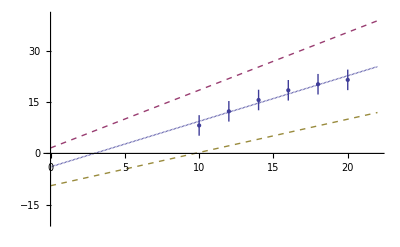

```mathematica
Show[Plot[Evaluate[{b*t+a,(b+Δb)*t+a+Δa,(b-Δb)*t+a-Δa}/.regerg],{t,0,22},PlotRange->{{0,22},{-20,40}},PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{.01}]}],ErrorListPlot[aufspaltung]]
```

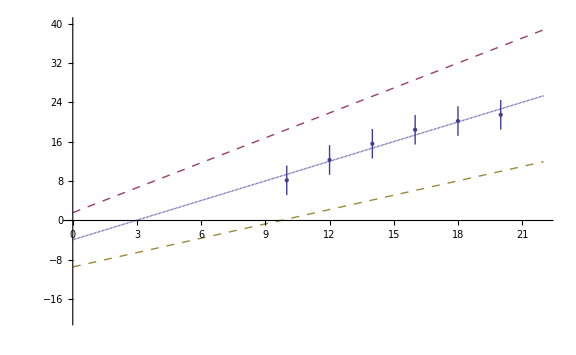

```mathematica
Show[%111,ImageSize->Large]
```

```mathematica
Show[%112,ImageSize->Full]
```